# Merged sequences Calculation of θ(t), dθ(t) and ν(t) dependences for heteropolymers with given sesquences and given product of transfer-matrices

## Preliminary chosen data and calculations

```mathematica
(*== Notes: 
F-> "f" in the program, c-> "conc, c" in the program, N -> "n"  in the program==*)

(*== Transfer matrix for heteropolymer: M[]  ==*)
M[d_,q_,W_]:=
Normal[SparseArray[{ {1,1}->W,{d-1,d}->(q-1),{d,d}->(q-1),{i_,j_}/;j-i==1-> 1,{d,j_}-> 1},{d,d}]]; 

(*==  Eigenvalues: λ for st-the highest value Subscript[λ, 1] second high value:Subscript[λ, 2]  ==*)
ML[d_,q_,W_]:=ML[d,q,W]=Eigenvalues[M[d,q,W]];(*λ*)
ML1[d_,q_,W_]:=Abs[ML[d,q,W][[1]]];(* Subscript[λ, 1]*)
ML2[d_,q_,W_]:=Abs[ML[d,q,W][[2]]]; (* Subscript[λ, 2]*)

(*==  Energetic parameter  ==*)
W[u_,t_]:=ⅇ^(u/t);



(*==  Correlation length  ==*)
Xi[d_,q_,W_]:=Abs[1/Log[ML1[d,q,W]/ML2[d,q,W]]];


(*==  Left matrix  &  right matrix  ==*)
MA[d_,q_,W_]:=Transpose[Eigenvectors[M[d,q,W]]];(*left matrix*)
MB[d_,q_,W_]:=Inverse[MA[d,q,W]];(*right matrix*)


(*==  Trasfer matrix of monomer in helix state: G' ==*)
 DW[d_,q_,W_]:=Normal[SparseArray[{ {1,1}->W},{d,d}]];  


(*== 2 differentials of characteristic equastion (L==λ -> variable) ==*)
dfdL[d_,L_, J_, Q_]:=L^(-1+d) (-ⅇ^J+L)+L^(-1+d) (L-Q)+(-1+d) L^(-2+d) (-ⅇ^J+L) (L-Q);
dfdJ[d_,L_, J_, Q_]:=ⅇ^J (1-Q)-ⅇ^J L^(-1+d) (L-Q);
dfdL[d_,q_,w_]:=dfdL[d,ML1[d,q,w],Log[w],q];dfdJ[d_,q_,w_]:=dfdJ[d,ML1[d,q,w],Log[w],q];


(*== Helicity degree: Theta1 and theta (different ways of calculation) ==*)
Theta1[d_,q_,W_]:=(MB[d,q,W]. DW[d,q,W].MA[d,q,W])[[1,1]]/ML1[d,q,W];
Theta[d_,q_,W_]:=-dfdJ[d,q,W]/dfdL[d,q,W]/ML1[d,q,W];
```

```mathematica
(*== values ==*)
(*== x-> probability of type A repeated units ,
	n0-> preliminary chosen number of repeated units,
	d-> transfer matrix dimension,
	u-> hydrogen bond's energy for A type and B type repeated units respectively-> u={Subscript[u, A],Subscript[u, B]},
	q-> number of conformations of repeated units: type A and type B respectively -> q={Subscript[q, A],Subscript[q, B]},
	t-> reduced temperature,
	data0 -> generating random sequence with probability "x"
 ==*)
d=4; u={1,0.8};q={71,51}; 

n=30000;ust={0.2,0.1};udst={0.1,0.2};
 qst={12,10}; qdst={10,12};
(* tmin=0.2; tmax=0.225; dt=(tmax-tmin)/500; look down for time propertie*)T={};
```

```mathematica
Creating an array of pseudorandom numbers corresponding to the sequences ;
seqord=RandomSample[Range[46,75],30]
```

{68,70,58,52,66,72,67,47,61,46,60,69,65,57,54,50,49,48,51,53,63,71,59,75,55,62,56,64,74,73}

```mathematica
(*-- Importing sequence --*)
seq1=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/68seq.dat"]];

(*-- Importing 2nd sequence --*)
seq2=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/70seq.dat"]];

(*-- Importing 3d sequence --*)
seq3=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/58seq.dat"]];
seq4=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/52seq.dat"]];
seq5=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/66seq.dat"]];
seq6=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/72seq.dat"]];
seq7=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/67seq.dat"]];
seq8=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/47seq.dat"]];
seq9=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/61seq.dat"]];
seq10=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/46seq.dat"]];

seq11=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/60seq.dat"]];
(*-- Importing 2nd sequence --*)
seq12=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/69seq.dat"]];

(*-- Importing 3d sequence --*)
seq13=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/65seq.dat"]];
seq14=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/57seq.dat"]];
seq15=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/54seq.dat"]];
seq16=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/50seq.dat"]];
seq17=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/49seq.dat"]];
seq18=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/48seq.dat"]];
seq19=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/51seq.dat"]];
seq20=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/53seq.dat"]];
seq21=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/63seq.dat"]];
(*-- Importing 2nd sequence --*)
seq22=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/71seq.dat"]];

(*-- Importing 3d sequence --*)
seq23=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/59seq.dat"]];
seq24=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/75seq.dat"]];
seq25=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/55seq.dat"]];
seq26=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/62seq.dat"]];
seq27=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/56seq.dat"]];
seq28=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/64seq.dat"]];
seq29=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/74seq.dat"]];
seq30=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/73seq.dat"]];


seqintr={};
(*--  merging sequences  --*)
AppendTo[seqintr,{seq1,seq2,seq3, seq4, seq5, seq6, seq7, seq8, seq9, seq10, seq11, seq12, seq13, seq14, seq15, seq16, seq17, seq18, seq19, seq20, seq21, seq22, seq23, seq24, seq25, seq26, seq27, seq28, seq29, seq30}];

(*-- making sequence as a normal matrix --*)
seq=Flatten[seqintr];

n=Length[seq];
```

```mathematica
conc=N[1/n Count[seq,0]]; (*concentration of type A nucleotides in the sequence*)

L1=ArrayFlatten[{{Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]],Normal[ SparseArray[{{1,1}-> 0},{d,d}]]}}];
R1=Flatten[{Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]],Normal[ SparseArray[{{1,1}-> 0},{d,d}]]},1];
R2=Flatten[{Normal[ SparseArray[{{1,1}-> 0},{d,d}]],Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]]},1];
```

```mathematica
Importing tensors for random sequences                                        ;

Htensor01=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/69Htr.dat"];
Htensor02=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/70Htr.dat"];
Htensor03=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/58Htr.dat"];
Htensor04=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/52Htr.dat"];
Htensor05=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/66Htr.dat"];
Htensor06=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/72Htr.dat"];
Htensor07=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/67Htr.dat"];
Htensor08=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/47Htr.dat"];
Htensor09=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/61Htr.dat"];
Htensor10=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/46Htr.dat"];
Htensor11=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/60Htr.dat"];
Htensor12=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/69Htr.dat"];
Htensor13=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/65Htr.dat"];
Htensor14=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/57Htr.dat"];
Htensor15=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/54Htr.dat"];
Htensor16=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/50Htr.dat"];
Htensor17=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/49Htr.dat"];
Htensor18=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/48Htr.dat"];
Htensor19=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/51Htr.dat"];
Htensor20=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/53Htr.dat"];
Htensor21=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/63Htr.dat"];
Htensor22=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/71Htr.dat"];
Htensor23=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/59Htr.dat"];
Htensor24=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/75Htr.dat"];
Htensor25=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/55Htr.dat"];
Htensor26=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/62Htr.dat"];
Htensor27=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/56Htr.dat"];
Htensor28=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/64Htr.dat"];
Htensor29=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/74Htr.dat"];
Htensor30=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/73Htr.dat"];
T0=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/T0.dat"];
(*--  defines matrices to fill later   --*)
θ={};ν={};Htr01={};Htr02={};Htr03={};Htr04={};Htr05={};Htr06={};Htr07={};Htr08={};Htr09={};Htr10={};Htr11={};
Htr12={}; 
Htr13={};
Htr14={};
Htr15={};
Htr16={};
Htr17={};
Htr18={};
Htr19={};
Htr20={};
Htr21={};
Htr22={}; 
Htr23={};Htr24={};Htr25={};Htr26={};Htr27={};Htr28={};Htr29={};Htr30={};omega={};fi={}; ka={};
```

```mathematica
Importing tensors for  sequences with correlation                                ;

Htensor01=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/118Htr.dat"];
Htensor02=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/115Htr.dat"];
Htensor03=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/152Htr.dat"];
Htensor04=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/154Htr.dat"];
Htensor05=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/119Htr.dat"];
Htensor06=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/143Htr.dat"];
Htensor07=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/142Htr.dat"];
Htensor08=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/141Htr.dat"];
Htensor09=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/155Htr.dat"];
Htensor10=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/148Htr.dat"];
Htensor11=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/116Htr.dat"];
Htensor12=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/145Htr.dat"];
Htensor13=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/151Htr.dat"];
Htensor14=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/157Htr.dat"];
Htensor15=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/146Htr.dat"];
Htensor16=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/147Htr.dat"];
Htensor17=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/150Htr.dat"];
Htensor18=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/156Htr.dat"];
Htensor19=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/112Htr.dat"];
Htensor20=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/120Htr.dat"];
Htensor21=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/117Htr.dat"];
Htensor22=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/111Htr.dat"];
Htensor23=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/114Htr.dat"];
Htensor24=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/113Htr.dat"];
Htensor25=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/153Htr.dat"];
Htensor26=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/144Htr.dat"];
Htensor27=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/160Htr.dat"];
Htensor28=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/158Htr.dat"];
Htensor29=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/159Htr.dat"];
Htensor30=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/149Htr.dat"];
T0=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/T.dat"];

(*--  defines matrices to fill later   --*)
θ={};ν={};Htr01={};Htr02={};Htr03={};Htr04={};Htr05={};Htr06={};Htr07={};Htr08={};Htr09={};Htr10={};Htr11={};
Htr12={}; 
Htr13={};
Htr14={};
Htr15={};
Htr16={};
Htr17={};
Htr18={};
Htr19={};
Htr20={};
Htr11={};
Htr12={}; 
Htr13={};Htr14={};Htr15={};Htr16={};Htr17={};Htr18={};Htr19={};Htr20={};omega={};fi={}; ka={};
```

```mathematica
Importing tensors for random sequences +solvent                                 ;

Htensor01=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/1Htr.dat"];
Htensor02=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/2Htr.dat"];
Htensor03=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/3Htr.dat"];
Htensor04=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/4Htr.dat"];
Htensor05=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/5Htr.dat"];
Htensor06=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/16Htr.dat"];
Htensor07=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/17Htr.dat"];
Htensor08=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/18Htr.dat"];
Htensor09=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/19Htr.dat"];
Htensor10=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/20Htr.dat"];
Htensor11=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/29Htr.dat"];
Htensor12=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/37Htr.dat"];
Htensor13=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/34Htr.dat"];
Htensor14=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/27Htr.dat"];
Htensor15=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/25Htr.dat"];
Htensor16=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/33Htr.dat"];
Htensor17=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/35Htr.dat"];
Htensor18=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/24Htr.dat"];
Htensor19=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/29Htr.dat"];
Htensor20=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/21Htr.dat"];

T0=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/T0.dat"];

(*tmin=T0[[1]]; tmax=T0[[-1]]; dt=(tmax-tmin)/1000;*)
(*--  defines matrices to fill later   --*)
θ={};ν={};Htr01={};Htr02={};Htr03={};Htr04={};Htr05={};Htr06={};Htr07={};Htr08={};Htr09={};Htr10={};Htr11={};
Htr12={}; 
Htr13={};Htr14={};Htr15={};Htr16={};Htr17={};Htr18={};Htr19={};Htr20={};omega={};fi={}; ka={};
```

```mathematica
Importing tensors for  sequences with correlation+solvent             ;

Htensor01=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/21Htr.dat"];
Htensor02=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/22Htr.dat"];
Htensor03=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/23Htr.dat"];
Htensor04=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/24Htr.dat"];
Htensor05=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/25Htr.dat"];
Htensor06=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/36Htr.dat"];
Htensor07=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/37Htr.dat"];
Htensor08=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/38Htr.dat"];
Htensor09=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/39Htr.dat"];
Htensor10=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/40Htr.dat"];
Htensor11=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/29Htr.dat"];
Htensor12=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/37Htr.dat"];
Htensor13=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/34Htr.dat"];
Htensor14=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/27Htr.dat"];
Htensor15=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/25Htr.dat"];
Htensor16=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/33Htr.dat"];
Htensor17=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/35Htr.dat"];
Htensor18=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/24Htr.dat"];
Htensor19=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/29Htr.dat"];
Htensor20=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/21Htr.dat"];

T0=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/T0.dat"];
T01=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/T30+.dat"];
(*tmin=T0[[1]]; tmax=T0[[-1]]; dt=(tmax-tmin)/1000;*)
(*--  defines matrices to fill later   --*)
θ={};ν={};Htr01={};Htr02={};Htr03={};Htr04={};Htr05={};Htr06={};Htr07={};Htr08={};Htr09={};Htr10={};Htr11={};
Htr12={}; 
Htr13={};Htr14={};Htr15={};Htr16={};Htr17={};Htr18={};Htr19={};Htr20={};omega={};fi={}; ka={};
```

## Main calculations in cycle

```mathematica
For[i=9,i<8009,i+=8,

(*== For every realisation separating "H" transfer matrices for each temperature to calculate "theta" later==*)
Htr01={};
AppendTo[Htr01,{Htensor01[[i-8]],Htensor01[[i-7]],Htensor01[[i-6]],Htensor01[[i-5]],Htensor01[[i-4]],Htensor01[[i-3]],Htensor01[[i-2]],Htensor01[[i-1]]}];
H1=10^-600*ArrayFlatten[Htr01,1];
Htr02={};
AppendTo[Htr02,{Htensor02[[i-8]],Htensor02[[i-7]],Htensor02[[i-6]],Htensor02[[i-5]],Htensor02[[i-4]],Htensor02[[i-3]],Htensor02[[i-2]],Htensor02[[i-1]]}];
H2=10^-600*ArrayFlatten[Htr02,1];

Htr03={};
AppendTo[Htr03,{Htensor03[[i-8]],Htensor03[[i-7]],Htensor03[[i-6]],Htensor03[[i-5]],Htensor03[[i-4]],Htensor03[[i-3]],Htensor03[[i-2]],Htensor03[[i-1]]}];
H3=10^-600*ArrayFlatten[Htr03,1];
Htr04={};
AppendTo[Htr04,{Htensor04[[i-8]],Htensor04[[i-7]],Htensor04[[i-6]],Htensor04[[i-5]],Htensor04[[i-4]],Htensor04[[i-3]],Htensor04[[i-2]],Htensor04[[i-1]]}];
H4=10^-600*ArrayFlatten[Htr04,1];
Htr05={};
AppendTo[Htr05,{Htensor05[[i-8]],Htensor05[[i-7]],Htensor05[[i-6]],Htensor05[[i-5]],Htensor05[[i-4]],Htensor05[[i-3]],Htensor05[[i-2]],Htensor05[[i-1]]}];
H5=10^-600*ArrayFlatten[Htr05,1];
Htr06={};
AppendTo[Htr06,{Htensor06[[i-8]],Htensor06[[i-7]],Htensor06[[i-6]],Htensor06[[i-5]],Htensor06[[i-4]],Htensor06[[i-3]],Htensor06[[i-2]],Htensor06[[i-1]]}];
H6=10^-600*ArrayFlatten[Htr06,1];
Htr07={};
AppendTo[Htr07,{Htensor07[[i-8]],Htensor07[[i-7]],Htensor07[[i-6]],Htensor07[[i-5]],Htensor07[[i-4]],Htensor07[[i-3]],Htensor07[[i-2]],Htensor07[[i-1]]}];
H7=10^-600*ArrayFlatten[Htr07,1];
Htr08={};
AppendTo[Htr08,{Htensor08[[i-8]],Htensor08[[i-7]],Htensor08[[i-6]],Htensor08[[i-5]],Htensor08[[i-4]],Htensor08[[i-3]],Htensor08[[i-2]],Htensor08[[i-1]]}];
H8=10^-600*ArrayFlatten[Htr08,1];
Htr09={};
AppendTo[Htr09,{Htensor09[[i-8]],Htensor09[[i-7]],Htensor09[[i-6]],Htensor09[[i-5]],Htensor09[[i-4]],Htensor09[[i-3]],Htensor09[[i-2]],Htensor09[[i-1]]}];
H9=10^-600*ArrayFlatten[Htr09,1];
Htr10={};
AppendTo[Htr10,{Htensor10[[i-8]],Htensor10[[i-7]],Htensor10[[i-6]],Htensor10[[i-5]],Htensor10[[i-4]],Htensor10[[i-3]],Htensor10[[i-2]],Htensor10[[i-1]]}];
H10=10^-600*ArrayFlatten[Htr10,1];

Htr11={};
AppendTo[Htr11,{Htensor11[[i-8]],Htensor11[[i-7]],Htensor11[[i-6]],Htensor11[[i-5]],Htensor11[[i-4]],Htensor11[[i-3]],Htensor11[[i-2]],Htensor11[[i-1]]}];
H11=10^-600*ArrayFlatten[Htr11,1];
Htr12={};
AppendTo[Htr12,{Htensor12[[i-8]],Htensor12[[i-7]],Htensor12[[i-6]],Htensor12[[i-5]],Htensor12[[i-4]],Htensor12[[i-3]],Htensor12[[i-2]],Htensor12[[i-1]]}];
H12=10^-600*ArrayFlatten[Htr12,1];
Htr13={};
AppendTo[Htr13,{Htensor13[[i-8]],Htensor13[[i-7]],Htensor13[[i-6]],Htensor13[[i-5]],Htensor13[[i-4]],Htensor13[[i-3]],Htensor13[[i-2]],Htensor13[[i-1]]}];
H13=10^-600*ArrayFlatten[Htr13,1];
Htr14={};
AppendTo[Htr14,{Htensor14[[i-8]],Htensor14[[i-7]],Htensor14[[i-6]],Htensor14[[i-5]],Htensor14[[i-4]],Htensor14[[i-3]],Htensor14[[i-2]],Htensor14[[i-1]]}];
H14=10^-600*ArrayFlatten[Htr14,1];
Htr15={};
AppendTo[Htr15,{Htensor15[[i-8]],Htensor15[[i-7]],Htensor15[[i-6]],Htensor15[[i-5]],Htensor15[[i-4]],Htensor15[[i-3]],Htensor15[[i-2]],Htensor15[[i-1]]}];
H15=10^-600*ArrayFlatten[Htr15,1];
Htr16={};
AppendTo[Htr16,{Htensor16[[i-8]],Htensor16[[i-7]],Htensor16[[i-6]],Htensor16[[i-5]],Htensor16[[i-4]],Htensor16[[i-3]],Htensor16[[i-2]],Htensor16[[i-1]]}];
H16=10^-600*ArrayFlatten[Htr16,1];
Htr17={};
AppendTo[Htr17,{Htensor17[[i-8]],Htensor17[[i-7]],Htensor17[[i-6]],Htensor17[[i-5]],Htensor17[[i-4]],Htensor17[[i-3]],Htensor17[[i-2]],Htensor17[[i-1]]}];
H17=10^-600*ArrayFlatten[Htr17,1];
Htr18={};
AppendTo[Htr18,{Htensor18[[i-8]],Htensor18[[i-7]],Htensor18[[i-6]],Htensor18[[i-5]],Htensor18[[i-4]],Htensor18[[i-3]],Htensor18[[i-2]],Htensor18[[i-1]]}];
H18=10^-600*ArrayFlatten[Htr18,1];
Htr19={};
AppendTo[Htr19,{Htensor19[[i-8]],Htensor19[[i-7]],Htensor19[[i-6]],Htensor19[[i-5]],Htensor19[[i-4]],Htensor19[[i-3]],Htensor19[[i-2]],Htensor19[[i-1]]}];
H19=10^-600*ArrayFlatten[Htr19,1];
Htr20={};
AppendTo[Htr20,{Htensor20[[i-8]],Htensor20[[i-7]],Htensor20[[i-6]],Htensor20[[i-5]],Htensor20[[i-4]],Htensor20[[i-3]],Htensor20[[i-2]],Htensor20[[i-1]]}];
H20=10^-600*ArrayFlatten[Htr20,1];

Htr21={};
AppendTo[Htr21,{Htensor21[[i-8]],Htensor21[[i-7]],Htensor21[[i-6]],Htensor21[[i-5]],Htensor21[[i-4]],Htensor21[[i-3]],Htensor21[[i-2]],Htensor21[[i-1]]}];
H21=10^-600*ArrayFlatten[Htr21,1];
Htr22={};
AppendTo[Htr22,{Htensor22[[i-8]],Htensor22[[i-7]],Htensor22[[i-6]],Htensor22[[i-5]],Htensor22[[i-4]],Htensor22[[i-3]],Htensor22[[i-2]],Htensor22[[i-1]]}];
H22=10^-600*ArrayFlatten[Htr22,1];
Htr23={};
AppendTo[Htr23,{Htensor23[[i-8]],Htensor23[[i-7]],Htensor23[[i-6]],Htensor23[[i-5]],Htensor23[[i-4]],Htensor23[[i-3]],Htensor23[[i-2]],Htensor23[[i-1]]}];
H23=10^-600*ArrayFlatten[Htr23,1];
Htr24={};
AppendTo[Htr24,{Htensor24[[i-8]],Htensor24[[i-7]],Htensor24[[i-6]],Htensor24[[i-5]],Htensor24[[i-4]],Htensor24[[i-3]],Htensor24[[i-2]],Htensor24[[i-1]]}];
H24=10^-600*ArrayFlatten[Htr24,1];
Htr25={};
AppendTo[Htr25,{Htensor25[[i-8]],Htensor25[[i-7]],Htensor25[[i-6]],Htensor25[[i-5]],Htensor25[[i-4]],Htensor25[[i-3]],Htensor25[[i-2]],Htensor25[[i-1]]}];
H25=10^-600*ArrayFlatten[Htr25,1];
Htr26={};
AppendTo[Htr26,{Htensor26[[i-8]],Htensor26[[i-7]],Htensor26[[i-6]],Htensor26[[i-5]],Htensor26[[i-4]],Htensor26[[i-3]],Htensor26[[i-2]],Htensor26[[i-1]]}];
H26=10^-600*ArrayFlatten[Htr26,1];
Htr27={};
AppendTo[Htr27,{Htensor27[[i-8]],Htensor27[[i-7]],Htensor27[[i-6]],Htensor27[[i-5]],Htensor27[[i-4]],Htensor27[[i-3]],Htensor27[[i-2]],Htensor27[[i-1]]}];
H27=10^-600*ArrayFlatten[Htr27,1];
Htr28={};
AppendTo[Htr28,{Htensor28[[i-8]],Htensor28[[i-7]],Htensor28[[i-6]],Htensor28[[i-5]],Htensor28[[i-4]],Htensor28[[i-3]],Htensor28[[i-2]],Htensor28[[i-1]]}];
H28=10^-600*ArrayFlatten[Htr28,1];
Htr29={};
AppendTo[Htr29,{Htensor29[[i-8]],Htensor29[[i-7]],Htensor29[[i-6]],Htensor29[[i-5]],Htensor29[[i-4]],Htensor29[[i-3]],Htensor29[[i-2]],Htensor29[[i-1]]}];
H29=10^-600*ArrayFlatten[Htr29,1];
Htr30={};
AppendTo[Htr30,{Htensor30[[i-8]],Htensor30[[i-7]],Htensor30[[i-6]],Htensor30[[i-5]],Htensor30[[i-4]],Htensor30[[i-3]],Htensor30[[i-2]],Htensor30[[i-1]]}];
H30=10^-600*ArrayFlatten[Htr30,1];

prod=ArrayFlatten[{{Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]],Normal[ SparseArray[{{1,1}-> 0},{d,d}]]},{Normal[ SparseArray[{{1,1}-> 0},{d,d}]],Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]]}}];
prod1=ArrayFlatten[{{Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]],Normal[ SparseArray[{{1,1}-> 0},{d,d}]]},{Normal[ SparseArray[{{1,1}-> 0},{d,d}]],Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]]}}];


(*--  for each t calculating multiplication of transfer-matrices (using product of transfer matrices for every realisation) to calculate helicity degree (θ) later  --*)




prod=prod.H1.H2.H3.H4.H5.H6.H7.H8.H9.H10.H11.H12.H13.H14.H15.H16.H17.H18.H19.H20.H21.H22.H23.H24.H25.H26.H27.H28.H29.H30;

(*--  for each t calculating multiplication of transfer-matrices (using product of transfer matrices for every realisation) to calculate average length of helix region (ν) later  --*)
(*  prod1=prod1.J1.J2.J3.J4.J5.J6.J7.J8.J9.J10; *)

(*-- calculating "Trace (Shpur)" of multiplication: "Left matrix","product of transfer-matrices" and "Right matrix" --*)
Ω=Tr[L1.prod.R1];
Ψ=Tr[L1.prod.R2]; 
(*  Κ=Tr[L1.prod1.R2];  *)

(*-- using "i" and calculating the right place for temperature value in matrix of temperatures  --*)
j=(i-1)/8;

T1=Flatten[T0[[j]]];

(*T1=Flatten[T01[[j]]];*)

(*--  Collecting θ(t) and ν(t) data respectively  --*)
AppendTo[θ,{T1[[1]],Θ=1/n*Ψ/Ω}];

(*  AppendTo[ν,{T1[[1]],nu=1/(1-Κ/Ψ)}];  *)
AppendTo[omega,Ω];
AppendTo[fi,Ψ]
(*  AppendTo[ka,Κ];  *)

]
```

```mathematica
Ω
```

9.26436763740819×10^5051

```mathematica
Ψ
```

9.3005144426817×10^5052

```mathematica
n
```

60000

## Graphs

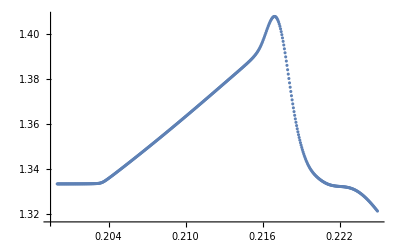

```mathematica
(*--  ν(t)dependence  --*)
nu1=ListPlot[ν]
```

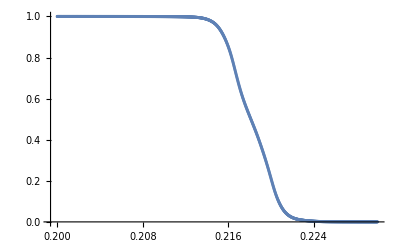

```mathematica
(*--  θ(t)dependence  --*)
T=ListPlot[θ]
```

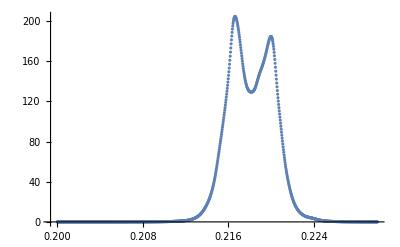

```mathematica
dθ=Table[{θ[[i,1]],-(θ[[i+1,2]]-θ[[i,2]])/(θ[[i+1,1]]-θ[[i,1]])},{i,Length[θ]-1}];

(*--  dθ(t)dependence  --*)
P=ListPlot[dθ, PlotRange->All]
```

## Exporting data

```mathematica
(*==  Exporting sequence  ==*)
strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/merged_seq/random/vacuum/" <>  DateString[Date[],{"merged_seq"}]<>".dat"];
WriteString[strm,ExportString[seq,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data θ(t)  --*)
strm=
OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/merged_seq/random/vacuum/" <>  DateString[Date[],{"theta_t_merged"}]<>".dat"];
WriteString[strm,ExportString[θ,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data dθ(t)  --*)strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/merged_seq/random/vacuum/" <>  DateString[Date[],{"dtheta_t_merged"}]<>".dat"];
WriteString[strm,ExportString[dθ,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data ν(t)  --*)strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/chem_phys/merged_seq/random/" <>  DateString[Date[],{"nu_t_merged"}]<>".dat"];
WriteString[strm,ExportString[ν,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data dθ(t)-correlation in the sequence  --*)strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/chem_phys/merged_seq/corr/" <>  DateString[Date[],{"dtheta_t_merged"}]<>".dat"];
WriteString[strm,ExportString[dθ,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*  export

/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/chem_phys/merged_seq/random/

/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/chem_phys/merged_seq/corr/

*)
```

```mathematica
(*   import

random - vacuum
/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/chem_phys/random_seq/data_vacuum/3seq.dat


random - solvent
/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/chem_phys/random_seq/data_solvent/3seq.dat


correlation - vacuum
/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/chem_phys/corr_seq/data_vacuum/1seq.dat

correlation - solvent
/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/chem_phys/corr_seq/data_solvent/1seq.dat

*)
```

```mathematica
Orderj={};
For[j=1,j<11, j+=1,
Ordj=RandomInteger[{1,20}];
AppendTo[Orderj,{Ordj}];
]
Order1=Flatten[Orderj[[]]]
```

```mathematica
{1,17,19,3,16,14,11,8,3,12}
```

```mathematica
Ordj
```

4

```mathematica
If[Ordj≠4,AppendTo[Orderj,{Ordj}], Ordj=RandomInteger[{1,10},1]]
```

```mathematica
{1}
```

```mathematica
Orderj[j-1]
```